```mathematica
a[x_]:=√(4.913+(0.1173+1.65*10^-8*z^2)/(x^2-(0.212+2.7*10^-8*z^2)^2)-0.0278*x^2)
b[x_]:=√(4.5455+2.605*10^-7*z^2+(0.097+2.7*10^-8*z^2)/(x^2-(0.201+5.4*10^-8*z^2)^2)-0.0224*x^2)
a[1.064]
a[2.128]
b[2.128]
```

2.23403

2.19399

2.11889

```mathematica
2.234031003585931
b[1.064]
```

2.23403

2.15287

{{z→-46.9287-6582.72 ⅈ},{z→-46.9287+6582.72 ⅈ},{z→46.9287-6582.72 ⅈ},{z→46.9287+6582.72 ⅈ},{z→5939.71},{z→-5939.71},{z→4092.18},{z→-4092.18}}

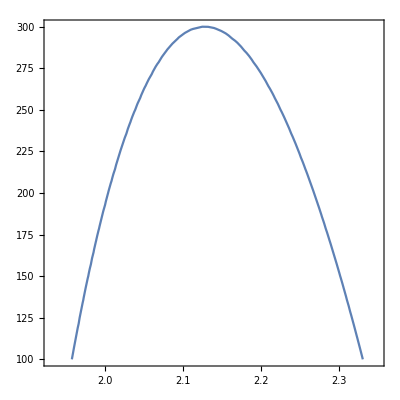

23662.2

$Aborted

-Graphics-

```mathematica
ne1[q_]:=1/(√((Cos[q])^2/(a[1.064])^2+(Sin[q])^2/(b[1.064])^2))
ne2[q_]:=1/(√((Cos[q])^2/(a[x])^2+(Sin[q])^2/(b[x])^2))
ne3[q_]:=1/(√((Cos[q])^2/(a[(1.064*x)/(x-1.064)])^2+(Sin[q])^2/(b[(1.064*x)/(x-1.064)])^2))
ContourPlot[ne1[1.03158]/1.064==ne2[1.03158]/x+ne3[1.03158]/((1.064*x)/(x-1.064))+1/(30(1+1.02*10^-5*(z-300))),{x,1.93,2.35},{z,100,300}]
```